# load SavedExpressions

in order given in SavedExpressionsTotalOrder.txt

Some functions are needed in definitions, so some order is needed.

New functions can be added at the bottom of the list.

```mathematica
Print["$SessionID=",$SessionID];(*identify notebooks running in this particular kernel (important for running multiple mma instances - recognize them by their messages window)*)
On@Assert;
Get[FileNameJoin@{NotebookDirectory[],"MathematicaOverloadings.m"}]
Needs@"Persist`"
Needs@"BoolEval`"
Needs@"GeneralUtilities`"
Needs@"SymbolicC`"
(*Needs@"PLYExport`"*)
Needs@"ExportTable`"

SetEnvironment["PATH"->StringJoin[Last@GetEnvironment[{"PATH"}],";C:\\Program Files\\MATLAB\\MATLAB Production Server\\R2015a\\bin\\win64"]]
SetEnvironment["PATH"->StringJoin[Last@GetEnvironment[{"PATH"}],";C:\\Programs\\MATLAB R2015a\\bin\\win64"]]
Needs@"MATLink`"
OpenMATLAB[]

SetEnvironment["NSIGHT_CUDA_DEBUGGER"->"1"];(*cannot hurt (except maybe performance)*)

Needs@"NotebookBackup`"
Needs@"CUDALink`"
Needs["CCompilerDriver`"]

Unprotect@Global`$extra;
ClearAll@Global`$extra;
Unprotect@BoxForm`$extra;
ClearAll@BoxForm`$extra;

$Path~AppendTo~NotebookDirectory[];
DepersistDef~Scan~Flatten@Import[FileNameJoin@{NotebookDirectory[],"SavedExpressionsTotalOrder.txt"},"Table"];
Off[GaussNewton::trace](*don't need this usually - TODO automatically disable by default all ::trace - message group? Note: MUST be called after GaussNewton has been loaded?*)


<<Combinatorica`
$ContextPath=$ContextPath~DeleteThenAppend~"Combinatorica`";
(*prefer built-in Graph[] object etc. over the Combinatorica variant*)
```

SetDelayed::write: Tag ImageMultiply in ImageMultiply[x_?NumericQ,i_Image] is Protected.

Set::write: Tag ImageMultiply in DownValues[ImageMultiply] is Protected.

extra$::shdw: Symbol extra$ appears in multiple contexts {BoxForm`,Global`}; definitions in context BoxForm` may shadow or be shadowed by other definitions.

Get::noopen: Cannot open C:\Users\Paul\Dropbox\Paul\MasterarbeitShared\Research\MathematicaLibraries\SavedExpressions\defFileWriteBytes.m.

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

## Gui and graphics

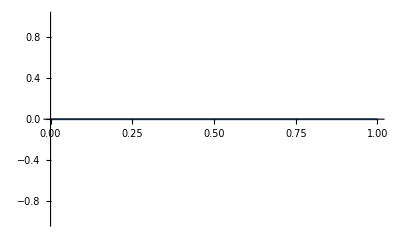

-Graphics3D-

```mathematica
(*load gui and plotting subsystems in FrontEnd (hangs it for a few seconds)*)
Manipulate[0,{x,0,1}]
Plot[0,{x,0,1}]
Plot3D[0,{x,0,1},{y,0,1}]
```

## Remote kernels

```mathematica
(*remote kernels [[*)
LaunchKernels[];(*local ones first, configure via gui = amount of logical processors*)

Needs["SubKernels`RemoteKernels`"]
Get@"tunnel.m"
(*Read: 
https://github.com/sakra/Tunnel/blob/master/MANUAL.md

get putty (installed! the script expects it somewhere) and Bitvise SSH server
make a virtual account on the Command Prompt shell, allowing opening of ports

make sure firewall is disabled on this network (?)

make sure remote computer is running and its ssh server too

ignore the empty commandline windows this opens

see $UserBaseDirectory\FrontEnd\Logs
*)
If[ComputerName[]=="PAULYOGA2PRO"
,LaunchKernels@RemoteMachineTunnel["PaulVirtual:123456@PAULSPC",12,"OperatingSystem"->"Windows"]

,(*else*)
Assert[ComputerName[]=="PAULSPC"];

LaunchKernels@RemoteMachineTunnel["PAULYOGA2PROVirtual:123456@PAULYOGA2PRO",4,"OperatingSystem"->"Windows","KernelPath"->"E:\\Programs\\Mathematica 11.0\\WolframKernel.exe"](*note the nonstandard installation path*)

]

(*]] end remote kernels*)
```

LinkObject::linkd: Unable to communicate with closed link LinkObject[3493@127.0.0.1,3494@127.0.0.1,5279,20].

Parallel`Developer`ConnectKernel::failinit: 1 of 4 kernels failed to initialize.

{KernelObject[13,PAULYOGA2PRO],KernelObject[14,PAULYOGA2PRO],KernelObject[16,PAULYOGA2PRO]}

```mathematica
Kernels[]//Length
```

15

```mathematica
ParallelEvaluate@$KernelID
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,16}